nucleon.calcBlock(prop_PDu,prop_PDd,112);

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/data

```mathematica
TomUp=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_up.gpl"],"# 0 0 0 0\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

```mathematica
TomDw=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_down.gpl"],"# 0 0 0 0\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

nucleon.calcBlock(prop_PDu,prop_PDu,112);

```mathematica
TomUp=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_up.gpl"],"# 0 0 0 0\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

```mathematica
TomDw=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_down.gpl"],"# 0 0 0 0\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

Two point function, matched !!!

```mathematica
Export["TwoPtFunc.wdx",MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]]
```

TwoPtFunc.wdx

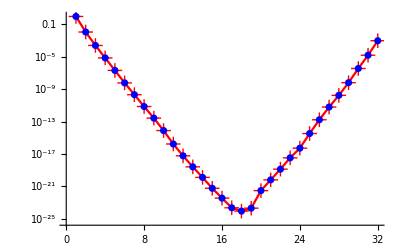

```mathematica
Show[{ListLogPlot[MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]//Re,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold]],ListLogPlot[2*#⟦2⟧&/@(TomUp+TomDw),PlotStyle->Blue]}]
```

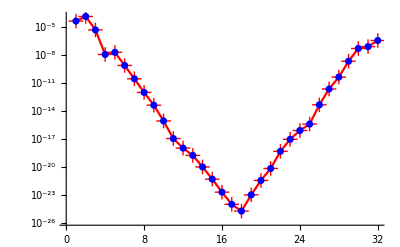

```mathematica
Show[{ListLogPlot[MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]//Im//Abs,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold]],ListLogPlot[2*#⟦3⟧&/@(TomUp+TomDw)//Abs,PlotStyle->Blue]}]
```

```mathematica
(2*#⟦2⟧&/@(TomUp+TomDw))/(MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]//Re)
```

{1.,1.,1.,0.999999,1.,1.,0.999999,1.,1.,0.999999,1.,1.,1.,1.,0.999998,1.,1.,1.,0.999996,1.,0.999998,1.,1.,0.999999,1.,1.,0.999999,1.,0.999998,1.,1.,1.}

```mathematica
(2*#⟦3⟧&/@(TomUp+TomDw))/(MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]//Im)
```

{0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,0.999998,0.999999,1.,1.,0.999994,1.,1.,0.999998,0.999999,1.,0.999998,1.,1.,1.,1.,1.,0.999998,1.}

3-point function, 0 steps in z

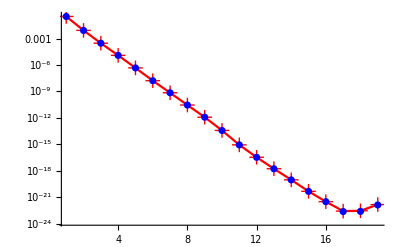

```mathematica
Show[{ListLogPlot[MmntmPrjctdtrPrpgtrs[u0in3TrcdPrpgtrs-d0in3TrcdPrpgtrs,{0,0,0}]//Re,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[2*#⟦2⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

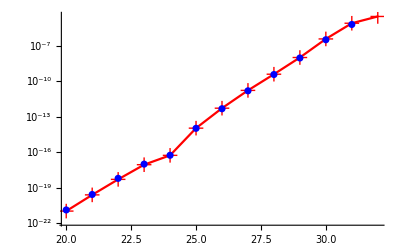

```mathematica
Show[{ListLogPlot[-MmntmPrjctdtrPrpgtrs[u0in3TrcdPrpgtrs-d0in3TrcdPrpgtrs,{0,0,0}]//Re,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[-2*#⟦2⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

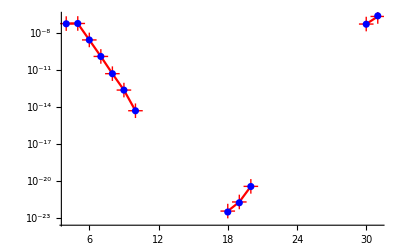

```mathematica
Show[{ListLogPlot[MmntmPrjctdtrPrpgtrs[u0in3TrcdPrpgtrs-d0in3TrcdPrpgtrs,{0,0,0}]//Im,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[2*#⟦3⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

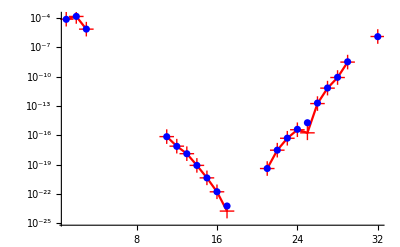

```mathematica
Show[{ListLogPlot[-MmntmPrjctdtrPrpgtrs[u0in3TrcdPrpgtrs-d0in3TrcdPrpgtrs,{0,0,0}]//Im,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[-2*#⟦3⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

```mathematica
(2*#⟦2⟧&/@(TomUp+TomDw))/(MmntmPrjctdtrPrpgtrs[u0in3TrcdPrpgtrs-d0in3TrcdPrpgtrs,{0,0,0}]//Re)
```

{0.985767,0.99082,0.99128,0.992464,0.99337,0.993465,0.994817,0.994563,0.994371,0.99341,0.990883,0.990842,0.989117,0.983782,0.987305,0.997399,0.88602,0.85574,0.903334,1.25001,1.07938,1.22,1.12022,1.01664,0.970667,0.898633,0.919069,0.940576,0.910086,0.854909,0.784567,-1.04278}

```mathematica
(2*#⟦3⟧&/@(TomUp+TomDw))/(MmntmPrjctdtrPrpgtrs[u0in3TrcdPrpgtrs-d0in3TrcdPrpgtrs,{0,0,0}]//Im)
```

{0.973357,1.01873,1.01289,0.958811,0.996137,0.994112,0.993968,0.993315,0.992455,0.99075,0.983342,0.956975,0.984746,0.989309,0.988962,1.01137,3.29258,0.840495,0.860564,0.976145,1.00557,1.0036,1.02914,1.10703,10.7362,1.12815,1.03814,1.05662,1.07133,0.970103,1.11833,0.966778}

```mathematica
(2*#⟦3⟧&/@(TomUp+0*TomDw))/(2*#⟦3⟧&/@(0*TomUp+TomDw))
```

{-3.0247,1.00549,1.0074,0.0533073,0.909512,0.961861,0.970684,0.952057,0.995223,0.882502,1.8433,1.39453,0.968294,0.861059,0.800373,0.88519,0.628396,5.56111,-4.67096,1.58371,0.0511215,0.972577,1.8633,1.53744,0.718243,0.217345,0.451358,0.376898,0.685881,0.870113,0.350323,0.159495}

```mathematica
Ratios[MmntmPrjctdtrPrpgtrs[#,{0,0,0}]&/@{u0in3TrcdPrpgtrs,d0in3TrcdPrpgtrs}]
```

(0.154894-0.0000147956 ⅈ | 0.483255-0.0000473942 ⅈ | 0.486433-0.000204899 ⅈ | 0.487912-0.0000205731 ⅈ | 0.489769-0.000117132 ⅈ | 0.490261+0.000217111 ⅈ | 0.491704+0.0000338133 ⅈ | 0.492159-0.000551297 ⅈ | 0.492369-0.000439507 ⅈ | 0.49379+0.00154497 ⅈ | 0.491551+0.00338863 ⅈ | 0.489395+0.00379692 ⅈ | 0.490978+0.00160197 ⅈ | 0.487495-0.000105044 ⅈ | 0.489292-0.00172668 ⅈ | 0.492989-0.00561824 ⅈ | 0.257689-0.248692 ⅈ | -0.233844+0.174828 ⅈ | 0.163492+0.191834 ⅈ | 0.531417+0.124513 ⅈ | 0.641159-0.0527758 ⅈ | 0.541412-0.0300218 ⅈ | 0.576711-0.0493946 ⅈ | 0.6119-0.0937297 ⅈ | 0.590805+0.04208 ⅈ | 0.554019-0.00329165 ⅈ | 0.556773-0.000515102 ⅈ | 0.563648+0.00559691 ⅈ | 0.581874+0.0125927 ⅈ | 0.603128-0.000540477 ⅈ | 0.66939+0.00866149 ⅈ | 0.950484-0.00170226 ⅈ)

3 point function, 1 step in z

```mathematica
TomUp=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_up.gpl"],"# 0 0 0 0\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

```mathematica
TomDw=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_down.gpl"],"# 0 0 0 0\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

3-point function, 1 steps in z

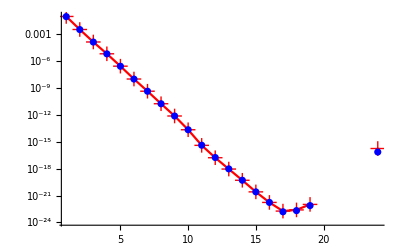

```mathematica
Show[{ListLogPlot[MmntmPrjctdtrPrpgtrs[u1in3TrcdPrpgtrs-d1in3TrcdPrpgtrs,{0,0,0}]//Re,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[2*#⟦2⟧&/@(TomUp+TomDw),Joined->False,PlotStyle->Blue,PlotRange->All]}]
```

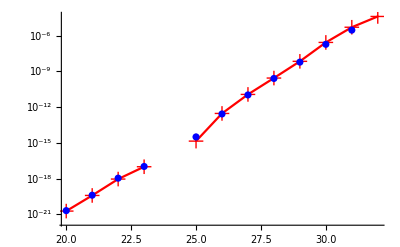

```mathematica
Show[{ListLogPlot[-MmntmPrjctdtrPrpgtrs[u1in3TrcdPrpgtrs-d1in3TrcdPrpgtrs,{0,0,0}]//Re,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[-2*#⟦2⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

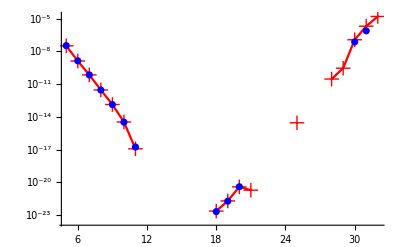

```mathematica
Show[{ListLogPlot[MmntmPrjctdtrPrpgtrs[u1in3TrcdPrpgtrs-d1in3TrcdPrpgtrs,{0,0,0}]//Im,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[2*#⟦3⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

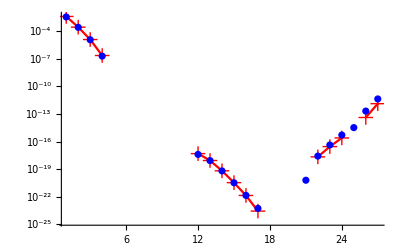

```mathematica
Show[{ListLogPlot[-MmntmPrjctdtrPrpgtrs[u1in3TrcdPrpgtrs-d1in3TrcdPrpgtrs,{0,0,0}]//Im,PlotStyle->Red,Joined->True,PlotMarkers->Style["+",15,Bold],PlotRange->All],ListLogPlot[-2*#⟦3⟧&/@(TomUp+TomDw),PlotStyle->Blue,PlotRange->All]}]
```

```mathematica
(2*#⟦2⟧&/@(TomUp+TomDw))/(MmntmPrjctdtrPrpgtrs[u1in3TrcdPrpgtrs-d1in3TrcdPrpgtrs,{0,0,0}]//Re)
```

{0.95765,0.977457,0.979986,0.983341,0.985054,0.988312,0.993869,0.994561,0.996238,0.996635,1.03261,1.05261,1.04506,1.00938,0.996972,1.00456,0.835697,0.831694,0.739172,1.09152,1.04966,1.19281,1.05399,0.408959,2.24827,0.903293,0.904278,0.925652,0.860023,0.695098,0.575262,-0.709769}

```mathematica
(2*#⟦3⟧&/@(TomUp+TomDw))/(MmntmPrjctdtrPrpgtrs[u1in3TrcdPrpgtrs-d1in3TrcdPrpgtrs,{0,0,0}]//Im)
```

{0.885383,0.955649,0.93987,0.858721,1.04495,1.03201,1.00112,0.987463,0.990714,0.971176,1.45154,0.818581,0.979249,0.972682,0.979256,1.0152,1.96244,0.89293,0.956907,1.02786,-3.2066,1.21268,1.49647,2.07848,-1.14188,4.9769,3.28243,-0.902719,-3.49049,0.644853,0.377729,-0.285926}

```mathematica
MmntmPrjctdtrPrpgtrs[d1in3TrcdPrpgtrs,{0,0,0}]/MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]
```

{1.+4.81115×10^-19 ⅈ,1.+1.38778×10^-17 ⅈ,1.+1.38778×10^-17 ⅈ,1.-2.23346×10^-17 ⅈ,1.-6.93889×10^-17 ⅈ,1.+0. ⅈ,1.+2.77556×10^-17 ⅈ,1.-2.77556×10^-17 ⅈ,1.+2.77556×10^-17 ⅈ,1.-1.52656×10^-16 ⅈ,1.+0. ⅈ,1.-1.38778×10^-16 ⅈ,1.+1.11022×10^-16 ⅈ,1.+2.22045×10^-16 ⅈ,1.-1.11022×10^-16 ⅈ,1.+2.77556×10^-16 ⅈ,1.-5.55112×10^-17 ⅈ,1.-3.88578×10^-16 ⅈ,1.-5.63438×10^-15 ⅈ,1.-1.11022×10^-15 ⅈ,1.+1.66533×10^-16 ⅈ,1.+6.38378×10^-16 ⅈ,1.+0. ⅈ,1.+1.9984×10^-15 ⅈ,1.+4.71845×10^-16 ⅈ,1.+1.11022×10^-16 ⅈ,1.+2.22045×10^-16 ⅈ,1.-2.77556×10^-17 ⅈ,1.+3.33067×10^-16 ⅈ,1.-5.55112×10^-17 ⅈ,1.-8.67362×10^-19 ⅈ,1.-1.34441×10^-17 ⅈ}

```mathematica
Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5"]
```

{/FH_quark_prpgtr/Im,/FH_quark_prpgtr/Re,/quark_prpgtrs/Im,/quark_prpgtrs/Re}

```mathematica
Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/quark_prpgtrs/Re"}]⟦11,2,1,3,45⟧
```

2.23167×10^-7

```mathematica
Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/FH_quark_prpgtr/Re"}]⟦2,2,1,1,17⟧
```

-0.000344764

```mathematica
Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/FH_quark_prpgtr/Re"}]⟦1,2,1,2,7⟧
```

-0.000249802

```mathematica
Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/d_tr_prpgtrs_Tom/Re"}]//Dimensions
```

{32,4,4,4}

```mathematica
Transpose[Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/d_tr_prpgtrs_Tom/Re"}]+I*Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/d_tr_prpgtrs_Tom/Im"}],{4,3,2,1}]⟦3,2,1,2⟧
```

2.69326×10^-7+4.5014×10^-8 ⅈ

```mathematica
d0in3TrcdPrpgtrs⟦3,2,1,2⟧
```

2.69326×10^-7+4.5014×10^-8 ⅈ

```mathematica
dtrprpgtrsPlDrcTom=Transpose[Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/d_tr_prpgtrs_PlDrc_Tom/Re"}]+I*Import["/Users/xiaonuxiong/Dropbox/GitHub/lattice_pion_pdf/hadron_PDFv2/proton_PDF_Tom.h5",{"Datasets","/d_tr_prpgtrs_PlDrc_Tom/Im"}],{4,3,2,1}];
```

```mathematica
MmntmPrjctdtrPrpgtrs[d1in3TrcdPrpgtrs,{0,0,0}]/MmntmPrjctdtrPrpgtrs[dtrprpgtrsPlDrcTom,{0,0,0}]
```

{1.-1.04083×10^-17 ⅈ,1.-4.16334×10^-17 ⅈ,1.-4.16334×10^-17 ⅈ,1.-5.20417×10^-18 ⅈ,1.-2.77556×10^-17 ⅈ,1.+0. ⅈ,1.+5.55112×10^-17 ⅈ,1.+0. ⅈ,1.+5.55112×10^-17 ⅈ,1.+1.38778×10^-16 ⅈ,1.-1.94289×10^-16 ⅈ,1.+8.32667×10^-17 ⅈ,1.+0. ⅈ,1.-1.11022×10^-16 ⅈ,1.-1.11022×10^-16 ⅈ,1.+2.77556×10^-16 ⅈ,1.+1.11022×10^-16 ⅈ,1.-3.34455×10^-15 ⅈ,1.-2.9976×10^-15 ⅈ,1.-8.88178×10^-16 ⅈ,1.+9.4369×10^-16 ⅈ,1.+2.22045×10^-16 ⅈ,1.+9.99201×10^-16 ⅈ,1.+2.22045×10^-16 ⅈ,1.+9.4369×10^-16 ⅈ,1.+0. ⅈ,1.+2.77556×10^-16 ⅈ,1.+2.77556×10^-16 ⅈ,1.+3.33067×10^-16 ⅈ,1.+1.80411×10^-16 ⅈ,1.-1.8735×10^-16 ⅈ,1.+9.02056×10^-17 ⅈ}

```mathematica
BlockRandom[SeedRandom[Method->{"MKL",Method->{"Sobol"}}];RandomInteger[{0,95},96]]
```

{37,85,61,13,19,67,91,43,31,79,55,7,10,58,82,34,46,94,70,22,16,64,88,40,28,76,52,4,3,51,75,27,39,87,63,15,21,69,93,45,33,81,57,9,6,54,78,30,42,90,66,18,12,60,84,36,24,72,48,0,0,48,72,24,36,84,60,12,18,66,90,42,30,78,54,6,9,57,81,33,45,93,69,21,15,63,87,39,27,75,51,3,5,53,77,29}

```mathematica
BlockRandom[SeedRandom[Method->{"MKL",Method->{"Sobol"}}];RandomInteger[{0,95},96]]
```

{83,59,11,8,56,80,32,44,92,68,20,14,62,86,38,26,74,50,2,1,49,73,25,37,85,61,13,19,67,91,43,31,79,55,7,10,58,82,34,46,94,70,22,16,64,88,40,28,76,52,4,3,51,75,27,39,87,63,15,21,69,93,45,33,81,57,9,6,54,78,30,42,90,66,18,12,60,84,36,24,72,48,0,0,48,72,24,36,84,60,12,18,66,90,42,30}

```mathematica
ttt={0,0,1024,1024,512,1536,1536,512,256,1280,1280,256,768,768,1792,1792,128,1920,1152,896,640,384,1664,1408,384,640,1408,1664,896,1152,1920,128,64,1088,1088,64,576,576,1600,1600,320,320,1344,1344,832,1856,1856,832,192,960,1216,1984,704,1472,1728,448,448,1728,1472,704,960,192,1984,1216,32,1632,1056,608,544,96,1568,1120,288,864,1312,1888,800,1376,1824,352,160,480,1184,1504,672,2016,1696,992,416,1248,1440,224,928,736,1952,1760,96,544,1120,1568,608,1056,1632,32,352,1824,1376,800,864,288,1888,1312,224,1440,1248,416,736,928,1760,1952,480,160,1504,1184,992,1696,2016,672,16,1360,1040,336,528,848,1552,1872,272,80,1296,1104,784,1616,1808,592,144,720,1168,1744,656,1232,1680,208,400,2000,1424,976,912,464,1936,1488,80,272,1104,1296,592,1808,1616,784,336,1040,1360,16,848,528,1872,1552,208,1680,1232,656,720,144,1744,1168,464,912,1488,1936,976,1424,2000,400,48,816,1072,1840,560,1328,1584,304,304,1584,1328,560,816,48,1840,1072,176,1200,1200,176,688,688,1712,1712,432,432,1456,1456,944,1968,1968,944,112,1904,1136,880,624,368,1648,1392,368,624,1392,1648,880,1136,1904,112,240,240,1264,1264,752,1776,1776,752,496,1520,1520,496,1008,1008,2032,2032,8,2040,1032,1016,520,504,1544,1528,264,760,1288,1784,776,1272,1800,248,136,120,1160,1144,648,1656,1672,632,392,1400,1416,376,904,888,1928,1912,72,952,1096,1976,584,1464,1608,440,328,1720,1352,696,840,184,1864,1208,200,1080,1224,56,712,568,1736,1592,456,312,1480,1336,968,1848,1992,824,40,408,1064,1432,552,1944,1576,920,296,1176,1320,152,808,664,1832,1688,168,1560,1192,536,680,24,1704,1048,424,792,1448,1816,936,1304,1960,280,104,1496,1128,472,616,984,1640,2008,360,216,1384,1240,872,1752,1896,728,232,600,1256,1624,744,1112,1768,88,488,1880,1512,856,1000,344,2024,1368,24,680,1048,1704,536,1192,1560,168,280,1960,1304,936,792,424,1816,1448,152,1320,1176,296,664,808,1688,1832,408,40,1432,1064,920,1576,1944,552,88,1768,1112,744,600,232,1624,1256,344,1000,1368,2024,856,1512,1880,488,216,360,1240,1384,728,1896,1752,872,472,1128,1496,104,984,616,2008,1640,56,1224,1080,200,568,712,1592,1736,312,456,1336,1480,824,1992,1848,968,184,840,1208,1864,696,1352,1720,328,440,1608,1464,584,952,72,1976,1096,120,136,1144,1160,632,1672,1656,648,376,1416,1400,392,888,904,1912,1928,248,1800,1272,776,760,264,1784,1288,504,520,1528,1544,1016,1032,2040,8,4,1028,1028,4,516,516,1540,1540,260,260,1284,1284,772,1796,1796,772,132,900,1156,1924,644,1412,1668,388,388,1668,1412,644,900,132,1924,1156,68,68,1092,1092,580,1604,1604,580,324,1348,1348,324,836,836,1860,1860,196,1988,1220,964,708,452,1732,1476,452,708,1476,1732,964,1220,1988,196,36,612,1060,1636,548,1124,1572,100,292,1892,1316,868,804,356,1828,1380,164,1508,1188,484,676,996,1700,2020,420,228,1444,1252,932,1764,1956,740,100,1572,1124,548,612,36,1636,1060,356,804,1380,1828,868,1316,1892,292,228,420,1252,1444,740,1956,1764,932,484,1188,1508,164,996,676,2020,1700,20,340,1044,1364,532,1876,1556,852,276,1108,1300,84,788,596,1812,1620,148,1748,1172,724,660,212,1684,1236,404,980,1428,2004,916,1492,1940,468,84,1300,1108,276,596,788,1620,1812,340,20,1364,1044,852,1556,1876,532,212,660,1236,1684,724,1172,1748,148,468,1940,1492,916,980,404,2004,1428,52,1844,1076,820,564,308,1588,1332,308,564,1332,1588,820,1076,1844,52,180,180,1204,1204,692,1716,1716,692,436,1460,1460,436,948,948,1972,1972,116,884,1140,1908,628,1396,1652,372,372,1652,1396,628,884,116,1908,1140,244,1268,1268,244,756,756,1780,1780,500,500,1524,1524,1012,2036,2036,1012,12,1020,1036,2044,524,1532,1548,508,268,1788,1292,764,780,252,1804,1276,140,1148,1164,124,652,636,1676,1660,396,380,1420,1404,908,1916,1932,892,76,1980,1100,956,588,444,1612,1468,332,700,1356,1724,844,1212,1868,188,204,60,1228,1084,716,1596,1740,572,460,1340,1484,316,972,828,1996,1852,44,1436,1068,412,556,924,1580,1948,300,156,1324,1180,812,1692,1836,668,172,540,1196,1564,684,1052,1708,28,428,1820,1452,796,940,284,1964,1308,108,476,1132,1500,620,2012,1644,988,364,1244,1388,220,876,732,1900,1756,236,1628,1260,604,748,92,1772,1116,492,860,1516,1884,1004,1372,2028,348,28,1708,1052,684,540,172,1564,1196,284,940,1308,1964,796,1452,1820,428,156,300,1180,1324,668,1836,1692,812,412,1068,1436,44,924,556,1948,1580,92,748,1116,1772,604,1260,1628,236,348,2028,1372,1004,860,492,1884,1516,220,1388,1244,364,732,876,1756,1900,476,108,1500,1132,988,1644,2012,620,60,204,1084,1228,572,1740,1596,716,316,1484,1340,460,828,972,1852,1996,188,1868,1212,844,700,332,1724,1356,444,588,1468,1612,956,1100,1980,76,124,1164,1148,140,636,652,1660,1676,380,396,1404,1420,892,1932,1916,908,252,780,1276,1804,764,1292,1788,268,508,1548,1532,524,1020,12,2044,1036,2,1542,1026,518,514,6,1538,1030,258,774,1282,1798,770,1286,1794,262,130,390,1154,1414,642,1926,1666,902,386,1158,1410,134,898,646,1922,1670,66,582,1090,1606,578,1094,1602,70,322,1862,1346,838,834,326,1858,1350,194,1478,1218,454,706,966,1730,1990,450,198,1474,1222,962,1734,1986,710,34,102,1058,1126,546,1638,1570,614,290,1382,1314,358,802,870,1826,1894,162,2022,1186,998,674,486,1698,1510,418,742,1442,1766,930,1254,1954,230,98,1062,1122,38,610,550,1634,1574,354,294,1378,1318,866,1830,1890,806,226,934,1250,1958,738,1446,1762,422,482,1702,1506,678,994,166,2018,1190,18,854,1042,1878,530,1366,1554,342,274,1622,1298,598,786,86,1810,1110,146,1238,1170,214,658,726,1682,1750,402,470,1426,1494,914,2006,1938,982,82,1814,1106,790,594,278,1618,1302,338,534,1362,1558,850,1046,1874,22,210,150,1234,1174,722,1686,1746,662,466,1430,1490,406,978,918,2002,1942,50,1334,1074,310,562,822,1586,1846,306,54,1330,1078,818,1590,1842,566,178,694,1202,1718,690,1206,1714,182,434,1974,1458,950,946,438,1970,1462,114,374,1138,1398,626,1910,1650,886,370,1142,1394,118,882,630,1906,1654,242,1782,1266,758,754,246,1778,1270,498,1014,1522,2038,1010,1526,2034,502,10,510,1034,1534,522,2046,1546,1022,266,1278,1290,254,778,766,1802,1790,138,1662,1162,638,650,126,1674,1150,394,894,1418,1918,906,1406,1930,382,74,1470,1098,446,586,958,1610,1982,330,190,1354,1214,842,1726,1866,702,202,574,1226,1598,714,1086,1738,62,458,1854,1482,830,970,318,1994,1342,42,1950,1066,926,554,414,1578,1438,298,670,1322,1694,810,1182,1834,158,170,30,1194,1054,682,1566,1706,542,426,1310,1450,286,938,798,1962,1822,106,990,1130,2014,618,1502,1642,478,362,1758,1386,734,874,222,1898,1246,234,1118,1258,94,746,606,1770,1630,490,350,1514,1374,1002,1886,2026,862,26,1198,1050,174,538,686,1562,1710,282,430,1306,1454,794,1966,1818,942,154,814,1178,1838,666,1326,1690,302,410,1582,1434,558,922,46,1946,1070,90,238,1114,1262,602,1774,1626,750,346,1518,1370,494,858,1006,1882,2030,218,1902,1242,878,730,366,1754,1390,474,622,1498,1646,986,1134,2010,110,58,718,1082,1742,570,1230,1594,206,314,1998,1338,974,826,462,1850,1486,186,1358,1210,334,698,846,1722,1870,442,78,1466,1102,954,1614,1978,590,122,1678,1146,654,634,142,1658,1166,378,910,1402,1934,890,1422,1914,398,250,270,1274,1294,762,1806,1786,782,506,1038,1530,14,1018,526,2042,1550,6,514,1030,1538,518,1026,1542,2,262,1794,1286,770,774,258,1798,1282,134,1410,1158,386,646,898,1670,1922,390,130,1414,1154,902,1666,1926,642,70,1602,1094,578,582,66,1606,1090,326,834,1350,1858,838,1346,1862,322,198,450,1222,1474,710,1986,1734,962,454,1218,1478,194,966,706,1990,1730,38,1122,1062,98,550,610,1574,1634,294,354,1318,1378,806,1890,1830,866,166,994,1190,2018,678,1506,1702,482,422,1762,1446,738,934,226,1958,1250,102,34,1126,1058,614,1570,1638,546,358,1314,1382,290,870,802,1894,1826,230,1954,1254,930,742,418,1766,1442,486,674,1510,1698,998,1186,2022,162,22,1874,1046,850,534,338,1558,1362,278,594,1302,1618,790,1106,1814,82,150,210,1174,1234,662,1746,1686,722,406,1490,1430,466,918,978,1942,2002,86,786,1110,1810,598,1298,1622,274,342,1554,1366,530,854,18,1878,1042,214,1170,1238,146,726,658,1750,1682,470,402,1494,1426,982,1938,2006,914,54,306,1078,1330,566,1842,1590,818,310,1074,1334,50,822,562,1846,1586,182,1714,1206,690,694,178,1718,1202,438,946,1462,1970,950,1458,1974,434,118,1394,1142,370,630,882,1654,1906,374,114,1398,1138,886,1650,1910,626,246,754,1270,1778,758,1266,1782,242,502,2034,1526,1010,1014,498,2038,1522,14,1530,1038,506,526,1018,1550,2042,270,250,1294,1274,782,1786,1806,762,142,634,1166,1658,654,1146,1678,122,398,1914,1422,890,910,378,1934,1402,78,442,1102,1466,590,1978,1614,954,334,1210,1358,186,846,698,1870,1722,206,1594,1230,570,718,58,1742,1082,462,826,1486,1850,974,1338,1998,314,46,922,1070,1946,558,1434,1582,410,302,1690,1326,666,814,154,1838,1178,174,1050,1198,26,686,538,1710,1562,430,282,1454,1306,942,1818,1966,794,110,2010,1134,986,622,474,1646,1498,366,730,1390,1754,878,1242,1902,218,238,90,1262,1114,750,1626,1774,602,494,1370,1518,346,1006,858,2030,1882,30,170,1054,1194,542,1706,1566,682,286,1450,1310,426,798,938,1822,1962,158,1834,1182,810,670,298,1694,1322,414,554,1438,1578,926,1066,1950,42,94,1258,1118,234,606,746,1630,1770,350,490,1374,1514,862,2026,1886,1002,222,874,1246,1898,734,1386,1758,362,478,1642,1502,618,990,106,2014,1130,62,1738,1086,714,574,202,1598,1226,318,970,1342,1994,830,1482,1854,458,190,330,1214,1354,702,1866,1726,842,446,1098,1470,74,958,586,1982,1610,126,650,1150,1674,638,1162,1662,138,382,1930,1406,906,894,394,1918,1418,254,1290,1278,266,766,778,1790,1802,510,10,1534,1034,1022,1546,2046,522};
```

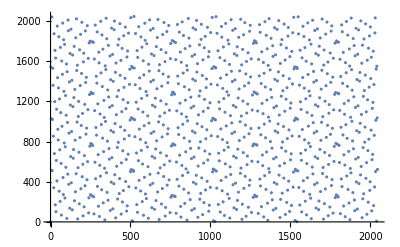

```mathematica
ListPlot[Transpose[{ttt⟦1;;-2;;2⟧,ttt⟦2;;-1;;2⟧}]]
```

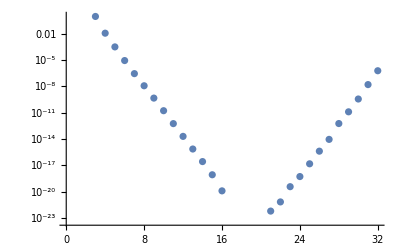

```mathematica
ListLogPlot[MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]//Re]
```

```mathematica
Append[{a,b,c,v},{d,e}]
```

{a,b,c,v,{d,e}}

```mathematica
TomUp=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_up.gpl"],"# 1 1 0 2\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

```mathematica
TomDw=StringReplace[("{{"<>StringReplace[StringDelete[Import[NotebookDirectory[]<>"nucleonCg5_down.gpl"],"# 1 1 0 2\n"],{"e"->"*^"," "->",","\n"->"},{"}]<>"}}"),",{},{},{}"->""]//ToExpression;
```

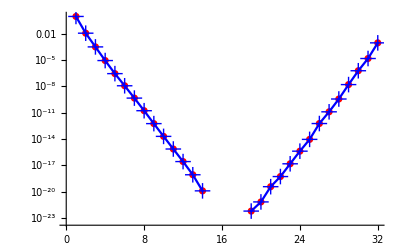

```mathematica
Show[{ListLogPlot[2*#⟦2⟧&/@(TomUp+TomDw),PlotStyle->Red]},ListLogPlot[Join[MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]⟦3;;-1⟧,-MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]⟦1;;2⟧]//Re,PlotStyle->Blue,PlotMarkers->Style["+", 16, Blue],Joined->True]]
```

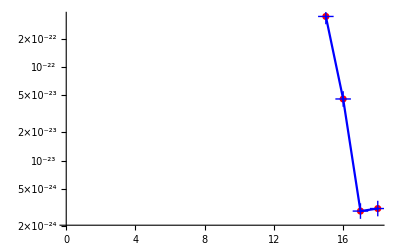

```mathematica
Show[{ListLogPlot[-2*#⟦2⟧&/@(TomUp+TomDw),PlotStyle->Red]},ListLogPlot[-Join[MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]⟦3;;-1⟧,-MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]⟦1;;2⟧]//Re,PlotStyle->Blue,PlotMarkers->Style["+", 16, Blue],Joined->True]]
```

```mathematica
Join[MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]⟦3;;-1⟧,-MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]⟦1;;2⟧]/(2*#⟦2⟧&/@(TomUp+TomDw))//Re
```

{1.,1.,1.,0.999999,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,0.999999,1.,1.,0.999998,1.,1.,1.,0.999998,1.,1.}

```mathematica
(2.1672100083+0.0000409342)*24
```

52.014

```mathematica
(2.1672100083-0.0000409342)*24
```

52.0121

```mathematica
52.0135/24
```

2.16723